# 26: Hessenberg Reduction:

We know the standard way to do QR.  Work your way through the columns of the matrix choosing v according to the fairly simple recipe in lecture 10 and make zeros using the Householder reflection H=I-2v⊗v until you run out of columns! The reason for doing this was to reduce A.x=b to a simpler triangular form.

We are going systematically make zeros using Householder reflections in a similarity transformation
	A->Q.A.Qᵀ	
that preserve eigenvalues.  The reason for doing this is to reduce A to a simpler form: eventually one that just lets you read the eigenvalues of the diagonal!

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}

## Optimistic Attempt

The plan is to make zeros in a matrix while not changing the eigenvalues!  To preserve the eigenvalues we need to use a similarity transformation
	A⟶Y.A.Y^-1
Since we are going to do a lot of matrix operations it is crucial that we use orthogonal similarity transformations
	A⟶Q.A.Qᵀ.
As an experiment we will see what happens if we try to zero an entire column and leave only the top element like we did before using our householder Q. Since the Householder Q is symmetric the Qᵀ=Q on the right does the same operations on the columns as Q on the left does on the rows.  As a result, similarity transformation destroys the zeros that were created in Q.A.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
Q=HouseMat[a1];
QA=Q.A; QAQtr=QA.Q;
TabView[{
"Q.A"->MatrixPlot[Chop[QA]],
"Q.A.Qᵀ"->MatrixPlot[Chop[QAQtr]]}]
```

12

This does not make zeros! It does however make matrices more Upper Triangular. The norm of strictly lower triangular portion divided by the norm of the entire thing is a reasonable way to measure degree of UTness!  We are going to use the Frobenius norm and note that since H is orthogonal the norm is unchanged by the similarity transformation!

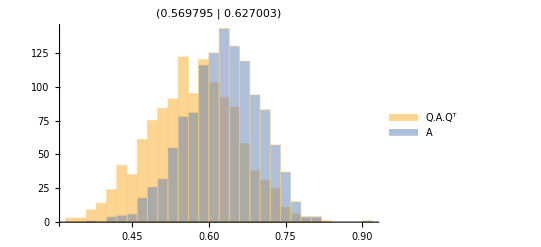

```mathematica
m=6;
SampleSize=1234;
Data=Table[
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
Q=HouseMat[a1];
QA=Q.A; QAQtr=QA.Qᵀ;
Map[Norm[LowerTriangularize[#,-1],"Frobenius"]&,{QAQtr,A}],
{SampleSize}]/Norm[A,"Frobenius"];
Histogram[Dataᵀ,20,ChartLegends->{"Q.A.Qᵀ","A"},PlotLabel->{Map[Mean,Dataᵀ]}]
```

We will come back to this!  For right now we want to make zeros that stay zeros!

## Realistic Attempt: Hessenberg Decomposition

The plan is to make zeros in a matrix while not changing the eigenvalues!  To preserve the eigenvalues we need to use a similarity transformation
	A⟶Y.A.Y^-1
Since we are going to do a lot of matrix operations it is crucial that we use orthogonal similarity transformations
	A⟶Q.A.Qᵀ.
As we saw it is too greedy to try to zero the whole column except the top element. However, if we try to zero everything except the top to elements we get zeros that are preserved.

This goes something like this.  Note that the H on the right makes zeros in the first column using rows 2 and above. It does not touch the first row! As a result, the Hᵀ=H on the left does not touch the first column and preserves the zeros that were just introduced!

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
v=Join[{0},HouseVec[a1⟦2;;-1⟧]];
Q=IdentityMatrix[m]-2 KroneckerProduct[v,v];
QA=Q.A; QAQtr=QA.Qᵀ;
TabView[{
"Q"->MatrixPlot[Q],
"Q.A"->MatrixPlot[Chop[QA]],
"Q.A.Qᵀ"->MatrixPlot[Chop[QAQtr]]}]
```

123

Sweeping down the columns in a loop produces an almost upper triangular matrix with a single lower diagonal.  Accumulating these reflections into a single orthogonal matrix Q gives a decomposition
	A=Q.H.Qᵀ
where the inner matrix is upper triangular with one extra non-zero lower diagonal.  The inner matrix is called a Hessenberg matrix.

The eigenvalues of H are the same as the eigenvalues of A.  You do not build the orthogonal Q unless you need the eigenvectors.  in fact, you never need to build the Householder matrices.  This is a Mathematica implementation of algorithm 26.1.

```mathematica
HessenbergReduction[AIn_]:= Module[{A=AIn, m=Length[A],x},
Do[
x=A⟦k+1;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧+Sign[x⟦1⟧]*Norm[x];
v=Normalize[v];
A⟦k+1;;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦k+1;;m,k;;m⟧];
A⟦1;;m,k+1;;m⟧=A⟦1;;m,k+1;;m⟧-2 KroneckerProduct[A⟦1;;m,k+1;;m⟧.v,v],
{k,1,m-2}];
Chop[A]]
```

As always test.

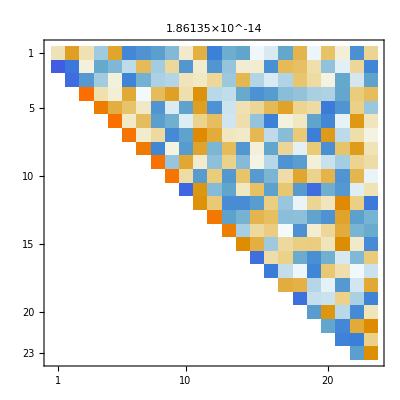

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}];
H=HessenbergReduction[A];
{λA,λH}=Map[Eigenvalues,{A,H}];
TableForm[{λA,λH}];
MatrixPlot[H,PlotLabel->Norm[λA-λH]]
```

If Q is needed as well we can accumulate the Q just like in the QR algorithm.  Every linear algebra tool has a Hessenberg reduction command.

## Symmetric Hessenberg Decomposition

The question is what happens if we run the Hessenberg decomposition on a symmetric matrix. Since all the operations preserve symmetry we get a Symmetric tri-diagonal matrix which can be stored as two vectors!

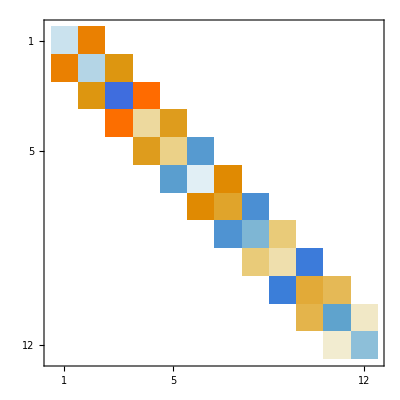

```mathematica
m=12;
S=RandomReal[{-1,1},{m,m}];S=S+Sᵀ;
H = Chop[HessenbergDecomposition[S]⟦2⟧];
MatrixPlot[H]
```

## Back to the earlier bad idea.

Householder reflections are good for introducing zeros in bulk. Remember Givens rotations
	(p1 | -p2
p2 | p1)
and 
	(p1 | -p2 | -p3 | -p4
p2 | p1 | -p4 | p3
p3 | p4 | p1 | -p2
p4 | -p3 | p2 | p1)
and
	(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | p4 | -p3 | p6 | -p5 | -p8 | p7
-p3 | -p4 | p1 | p2 | p7 | p8 | -p5 | -p6
-p4 | p3 | -p2 | p1 | p8 | -p7 | p6 | -p5
-p5 | -p6 | -p7 | -p8 | p1 | p2 | p3 | p4
-p6 | p5 | -p8 | p7 | -p2 | p1 | -p4 | p3
-p7 | p8 | p5 | -p6 | -p3 | p4 | p1 | -p2
-p8 | -p7 | p6 | p5 | -p4 | -p3 | p2 | p1)
are orthogonal for unit vectors.

#### Traditional G_2

The top corner of a Hessenberg matrix A looks like 
	(A_TL | A_TR
0 | A_BR)
Where A_BR=A_(3:m,3:m) is upper Hessenberg, A_TR=A_(1:2,3:m) is general rectangular and  
	A_TL=A_(1:2,1:2)=(A_11 | A_12
A_21 | A_22).
Computing Q.A with the Givens rotation
	Q=(G_2 | 0
0 | I_(m-2))=((p_1 | -p_2
p_2 | p_1) | 0
0 | I_(m-2))
gives
	Q.A=(G_2.A_TL | G_2.A_TR
0 | A_BR)
and very specifically
	G_2.A_TL=(p_1 | -p_2
p_2 | p_1).(A_11 | A_12
A_21 | A_22)=(A_11 p_1-A_21 p_2 | A_12 p_1-A_22 p_2
A_21 p_1+A_11 p_2 | A_22 p_1+A_12 p_2)
We can zero the boxed entry by choosing {p_1,p_2} to be a unit vector perpendicular to {A_11,A_12}: there are two easily computable choices.

Of course, we actually need 
	Q.A.Qᵀ=(G_2.A_TL | G_2.A_TR
0 | A_BR)(G_2 ᵀ | o
0 | I_(m-2))=(G_2.A_TL.G_2 ᵀ | G_2.A_TR
0 | A_BR)
so we look at 
	G_2.A_TL.G_2 ᵀ=(p_1 | -p_2
p_2 | p_1).(A_11 | A_12
A_21 | A_22).(p_1 | p_2
-p_2 | p_1)=(A_11 p_1^2+p_2 (-A_12 p_1-A_21 p_1+A_22 p_2) | A_12 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_21 p_2)
A_21 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_12 p_2) | A_22 p_1^2+p_2 (A_12 p_1+A_21 p_1+A_11 p_2))
This is nearer upper triangular if the lower left entry
	A_21 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_12 p_2)
is small.  We can not forget about the constraint!  If we choose p={A_12,-A_11}/√(A_12^2+A_11^2) we get

```mathematica
MatrixForm[Simplify[({{Subscript[p, 1], -Subscript[p, 2]}, {Subscript[p, 2], Subscript[p, 1]}}).({{Subscript[A, 11], Subscript[A, 12]}, {Subscript[A, 21], Subscript[A, 22]}}).({{Subscript[p, 1], Subscript[p, 2]}, {-Subscript[p, 2], Subscript[p, 1]}})]]
```

(A_11 p_1^2+p_2 (-A_12 p_1-A_21 p_1+A_22 p_2) | A_12 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_21 p_2)
A_21 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_12 p_2) | A_22 p_1^2+p_2 (A_12 p_1+A_21 p_1+A_11 p_2))

```mathematica
F[p_,A_]:=Abs[p⟦1⟧^2 A⟦2,1⟧-p⟦2⟧ (-p⟦1⟧ A⟦1,1⟧+p⟦2⟧ A⟦1,2⟧+p⟦1⟧ A⟦2,2⟧)]
A=RandomReal[{-1,1},{2,2}]; 
pRand=Normalize[RandomReal[{-1,1},2]];
pZero=Normalize[{A⟦1,2⟧,-A⟦1,1⟧}];
pNothing={1,0};
Map[F[#,A]&,{pRand,pZero,pNothing}]
```

{0.615976,0.638132,0.756569}

```mathematica
Subscript[A, 21] Subscript[p, 1]^2-Subscript[p, 2] (-Subscript[A, 11] Subscript[p, 1]+Subscript[A, 22] Subscript[p, 1]+Subscript[A, 12] Subscript[p, 2])/.{Subscript[A, 11]->A⟦1,1⟧,Subscript[A, 12]->A⟦1,2⟧,Subscript[A, 21]->A⟦2,1⟧,Subscript[A, 22]->A⟦2,2⟧,Subscript[p, 1]->p⟦1⟧,Subscript[p, 2]->p⟦2⟧}
```

Part::partd: Part specification A⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification A⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification A⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

p⟦1⟧^2 A⟦2,1⟧-p⟦2⟧ (-p⟦1⟧ A⟦1,1⟧+p⟦2⟧ A⟦1,2⟧+p⟦1⟧ A⟦2,2⟧)

```mathematica
¶Consider t¶
```

```mathematica
T=SparseArray[{
Band[{1,1}]->Array[d,4],
Band[{1,2}]->Array[u,3],
Band[{2,1}]->Array[u,3]}];
Mat=Simplify[({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}}).T.Transpose[({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}})]];
Total[Diagonal[Mat]^2]
```

(p3^2 d[1]+p4^2 d[2]+p1^2 d[3]+p2^2 d[4]+2 p3 p4 u[1]+2 p1 p4 u[2]-2 p1 p2 u[3])^2+(p4^2 d[1]+p3^2 d[2]+p2^2 d[3]+p1^2 d[4]-2 p3 p4 u[1]-2 p2 p3 u[2]+2 p1 p2 u[3])^2+(p2^2 d[1]+p1^2 d[2]+p4^2 d[3]+p3^2 d[4]+2 p1 p2 u[1]-2 p1 p4 u[2]-2 p3 p4 u[3])^2+(p1^2 d[1]+p2^2 d[2]+p3^2 d[3]+p4^2 d[4]-2 p1 p2 u[1]+2 p2 p3 u[2]+2 p3 p4 u[3])^2

```mathematica
MatrixForm[Simplify[LowerTriangularize[Mat,-1]]]
```

(0 | 0 | 0 | 0
p1 p2 (d[1]-d[2])+p3 p4 (d[3]-d[4])+p1^2 u[1]-p2^2 u[1]-p1 p3 u[2]+p2 p4 u[2]-p3^2 u[3]+p4^2 u[3] | 0 | 0 | 0
-p3 p4 u[2]+p2 (-p4 d[2]+p4 d[4]-p3 u[1]+p3 u[3])+p1 (p3 (d[1]-d[3])+p4 u[1]-p2 u[2]-p4 u[3]) | p1 p4 (d[2]-d[3])+p2 p3 (d[1]-d[4])+p1^2 u[2]-p4^2 u[2]+p1 p3 (u[1]+u[3])+p2 p4 (u[1]+u[3]) | 0 | 0
p2 p3 (d[2]-d[3])+p1 p4 (d[1]-d[4])-p2^2 u[2]+p3^2 u[2]-p1 p3 (u[1]+u[3])-p2 p4 (u[1]+u[3]) | p3 p4 u[2]+p2 (p4 (d[1]-d[3])-p3 u[1]+p1 u[2]+p3 u[3])+p1 (-p3 d[2]+p3 d[4]+p4 u[1]-p4 u[3]) | p3 (p4 d[1]-p3 u[1])+p4 (-p3 d[2]+p4 u[1]+p2 u[2])+p1 (p2 d[3]-p3 u[2]+p1 u[3])-p2 (p1 d[4]+p2 u[3]) | 0)

```mathematica
m=12;
S=RandomReal[{-1,1},{m,m}];S=S+Sᵀ;
H = Chop[HessenbergDecomposition[S]⟦2⟧];
MatrixPlot[H]
```

-Graphics-